```mathematica
(***  GIG_GNIG is a Mathematica Notebook which has modules to be used in the computation of the GIG and GNIG pdf's, cdf's and quantiles.
The user functions are:
GIGpdf, GIGcdf, GIGquant, GNIGpdf, GNIGcdf and GNIGquant,
on which help may be obtained by typing ?GIGpdf, ?GIGcdf, ?QuantGIG, ?GNIGpdf and ?GNIGcdf
***)

(***  GIG  ***)

Rat[x_]:=Module[{nn},
If [ToString[Head[x]]≠"Real",x,
nn=StringLength[ToString[x,InputForm]]-1;Round[x*10^nn]/10^nn]]

SetAttributes[Rat,Listable]

Makec[r_,l_,p_]:=Module[{c},
c=Table[Table[1,{j,1,Max[r]}],{i,1,p}];
Do[c[[i,r[[i]]]]=Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,1,i-1}]*Product[(l[[j]]-l[[i]])^(-r[[j]]),{j,i+1,p}]/(r[[i]]-1)!,{i,1,p}];
Do[Do[c[[i,r[[i]]-k]]=Sum[((r[[i]]-k+j-1)!*(Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,1,i-1}]+Sum[r[[h]]/(l[[i]]-l[[h]])^j,{h,i+1,p}])*c[[i]][[r[[i]]-(k-j)]])/(r[[i]]-k-1)!,{j,1,k}]/k,{k,1,r[[i]]-1}],{i,1,p}];
c]

GIGpdfcomp[r_,li_,zi_,prec_:150]:=Module[{p,l,c,z},
If[Count[r,_Integer]==Length[r]&&And@@NonNegative[r]&&And@@Positive[li]&&Length[r]==Length[li],
If[zi>0,
p=Length[r];l=Rat[li];c=Makec[r,l,p];z=Rat[zi];
SetPrecision[Product[l[[j]]^r[[j]],{j,1,p}]*Sum[Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec],If[zi==0,0,Print["Third argument must be a non-negative value"]]]]]

GIGpdf[r_,l_,ww_,prec_:150,precp_:20] :=Module[{newprec},
newprec=prec;
If[prec==Null,newprec=150];
SetPrecision[GIGpdfcomp[r,l,ww,newprec],precp] ]

GIGpdf::usage="GIGpdf[r, l, z, prec] gives the value for the pdf of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l', computed at the point 'z', with 'prec' digits of precision (default value: 150) and displayed with 'precp' digits (default value:20) - the first 3 arguments are mandatory and the last two are optional";

GIGcdfcomp[r_,li_,zi_,prec_:150]:=Module[{p,l,c,z},
If[Count[r,_Integer]==Length[r]&&And@@NonNegative[r]&&And@@Positive[li]&&Length[r]==Length[li],
If[zi>0,
p=Length[r];l=Rat[li];c=Makec[r,l,p];z=Rat[zi];
1-Product[l[[j]]^r[[j]],{j,1,p}]*SetPrecision[Sum[Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec],If[zi==0,0,Print["Third argument must be a non-negative value"]]]]]

GIGcdf[r_,l_,ww_,prec_:150,precp_:20] :=Module[{newprec},
newprec=prec;
If[prec==Null,newprec=150];
SetPrecision[GIGcdfcomp[r,l,ww,newprec],precp] ]

GIGcdf::usage="GIGcdf[r, l, z, prec] gives the value for the cdf of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l', computed at the point 'z', with 'prec' digits of precision (default value: 150) and displayed with 'precp' digits (default value:20) - the first 3 arguments are mandatory and the last two are optional";

GIGquant[r_,l_,qquant_,eps_:10^-11,preco_:50,xoo_:1,ind_:0]:=Module[{quant,xo,prec,vec,p,ll,c,pr,xa,xb,res,nx,F,F1,F2},
quant=Rat[qquant];
If[TrueQ[xoo==1||xoo==Null],xo=1,xo=Rat[xoo]];
prec=preco;
p=Length[r];
ll=Rat[l];
c=Makec[r,ll,p];
pr=Product[ll[[j]]^r[[j]],{j,1,p}];
F[x_]=GIGcdfsimpfast[r,ll,x,p,pr,c];
While[Length[RealDigits[res=SetPrecision[F[xo],prec]][[1]]]<preco,prec=3*prec];
If[res>quant,xa=xo;xo=xo/2;While[SetPrecision[F[xo],prec]>quant,xa=xo;xo=xo/2],
xa=xo;xo=xo*2;While[SetPrecision[F[xo],prec]<quant,xa=xo;xo=xo*2]];
If[xo>xa,xb=xo,xb=xa;xa=xo];
xo=(xa+xb)/2;
res=SetPrecision[F[xo],prec];
While[Abs[res-quant]>Min[10^-3,quant/10],xo=(xa+xb)/2;
If[(res=SetPrecision[F[xo],prec])>quant,xb=xo,xa=xo]];
nx=Rat[xo];
xa=0;
If[ind==0||ind==Null,{F1[x_]=GIGpdfsimpfast[r,ll,x,p,pr,c];
While[Abs[nx-xa]>eps,{xa=nx;
nx=xa+(quant-SetPrecision[F[xa],prec])/SetPrecision[F1[xa],prec]}]},
{F1[x_]=GIGpdfsimp[r,ll,x,p,pr,c,prec];
F2[x_]=GIGcdfsimp[r,ll,x,p,pr,c,prec];
While[Abs[nx-xa]>eps,{xa=nx;nx=xa+(quant-F2[Rat[xa]])/F1[Rat[xa]]}]}];SetPrecision[nx,Max[preco,-Log[10,eps]]]]

GIGquant::usage="GIGquant [r,  l,  q,  eps,  prec,  xo,  ind]
Gives the value for the quantile 'q' of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l';
Mandatory arguments:
'r' - list of shape parameters;
'l' - list of rate parameters;
'q' - required quantile (value between 0 and 1);
Optional arguments are:
'eps' - value for the largest difference between consecutive iteration values for the approximate quantile (has a default value of 10^-11);
'prec' - number of digits of precision for computations and printing the quantile value (default value: maximum between 50 and -Log10 of 'eps');
'xo' - initial value for the search of the quantile (default value: 1) and usually there is no need to change this value since the module is sturdy enough to be able to search for good initial values;
'ind' - index which has a default value of zero and if set to a different value will make the module to take an even more precise path of computation";

GIGpdfsimp[r_,l_,zi_,p_,pr_,c_,prec_:50]:=Module[{z},
z=Rat[zi];
SetPrecision[pr*Sum[Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec]]

GIGcdfsimp[r_,l_,zi_,p_,pr_,c_,prec_:50]:=Module[{z},
z=Rat[zi];
1-pr*SetPrecision[Sum[Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}],prec]]

GIGpdfsimpfast[r_,l_,z_,p_,pr_,c_]:=
pr*Sum[Sum[c[[j]][[k]]*z^(k-1),{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}]

GIGcdfsimpfast[r_,l_,z_,p_,pr_,c_]:=
1-pr*Sum[Sum[c[[j]][[k]]*(k-1)!*Sum[z^i/(i!*l[[j]]^(k-i)),{i,0,k-1}],{k,1,r[[j]]}]*Exp[-l[[j]]*z],{j,1,p}]



(***  GNIG   ***)

Hgeo[b_,k_,x_]:=Module[{F11,F12,F21,F22,F31,F32,res,gg,gg2,rr},
F11=1;
F12=0;
F21=0;
F22=b;
res=Table[0,{j,1,k}];
rr=Re[(-x)^(-b)*(Gamma[b]-Gamma[b,-x])];
res[[1]]=b*rr;
Do[
{F31=(b+j)/(x*j)*((x+b+j-1)*F21-(b+j-1)*F11);
F32=(b+j)/(x*j)*((x+b+j-1)*F22-(b+j-1)*F12);
F11=F21;
F12=F22;
F21=F31;
F22=F32;
res[[j+1]]=F31*Exp[x]+F32*rr},{j,1,k-1}];
res
]

GNIGpdfcomp[r_,bb_,l_,aa_,ww_,prec_:150] := Module[{g,P,a,b,ll,c,w},
 If[Count[r,_Integer]==Length[r] && And@@NonNegative[r] && And@@Positive[l],
If[ww>0,
g = Length[r];
w=Rat[ww];
ll=Rat[l];
a=Rat[aa];
b=Rat[bb];
c =Makec[r,ll,g];
resn=SetPrecision[Table[Hgeo[b,r[[j]],-(a-ll[[j]])*w],{j,1,g}],prec];
SetPrecision[Product[ll[[j]]^r[[j]], {j, 1, g}]*a^b*Sum[Exp[-ll[[j]]*w]*Sum[c[[j]][[k]]*
         Gamma[k]/Gamma[k+b]*w^(k+b-1)*resn[[j,k]],
         {k,1,r[[j]]}],{j, 1, g}],prec],If[ww==0,0,Print["The running value has to be a non-negative value"]]]
 ] ]

GNIGpdf[r_,bb_,l_,aa_,ww_,prec_:150,precp_:20] :=Module[{newprec},
newprec=prec;
If[prec==Null,newprec=150];
SetPrecision[GNIGpdfcomp[r,bb,l,aa,ww,newprec],precp] ]

GNIGpdf::usage="GNIGpdf[r, r2, ll, ll2, z, prec, precp] gives the value for the pdf of a GNIG distribution with a set of integer shape parameters 'r' and non-integer shape parameter 'r2', and rate parameters 'll', corresponding to the integer shape parameters, and shape parameter 'll2', corresponding to the non-integer shape parameter, computed at the point 'z', computed with precision a precision of 'prec' digits (default value: 150) and displayed with 'precp' digits (default value: 20) - the first 5 arguments are mandatory and the last two are optional";

GNIGcdfcomp[r_,bb_,l_,aa_,ww_,prec_:150] := Module[{g,P,a,b,ll,c,w,resn},
If[Count[r,_Integer]==Length[r] && And@@NonNegative[r] && And@@Positive[l],
If[ww>0,
g = Length[r];
w=Rat[ww];
ll=Rat[l];
a=Rat[aa];
b=Rat[bb];
c = Makec[r,ll,g];
resn=SetPrecision[Table[Hgeo[b,r[[j]],-(a-ll[[j]])*w],{j,1,g}],prec];
SetPrecision[a^b*w^b/Gamma[b+1]*Hypergeometric1F1[b,b+1,-a w]-Product[ll[[j]]^r[[j]], {j, 1, g}]*a^b*Sum[Exp[-ll[[j]]*w]*Sum[c[[j]][[k]]/ll[[j]]^k*(k-1)!*
    Sum[w^(b+i)*ll[[j]]^i/Gamma[b+1+i]*
         resn[[j,i+1]],{i,0,k-1}],{k,1,r[[j]]}],
         {j, 1, g}],prec],If[ww==0,0,Print["The running value has to be a non-negative value"]]]
 ] ]

GNIGcdf[r_,bb_,l_,aa_,ww_,prec_:150,precp_:20] :=Module[{newprec},
newprec=prec;
If[prec==Null,newprec=150];
SetPrecision[GNIGcdfcomp[r,bb,l,aa,ww,newprec],precp] ]

GNIGcdf::usage="GNIGpdf[r, r2, ll, ll2, z, prec, precp] gives the value for the Cdf of a GNIG distribution with a set of integer shape parameters 'r' and non-integer shape parameter 'r2', and rate parameters 'll', corresponding to the integer shape parameters, and shape parameter 'll2', corresponding to the non-integer shape parameter, computed at the point 'z', computed with precision a precision of 'prec' digits (default value: 150) and displayed with 'precp' digits (default value: 20) - the first 5 arguments are mandatory and the last two are optional";

GNIGpdfsimp[r_,b_,l_,a_,zi_,g_,pr_,c_,prec_:150]:=Module[{w,resn},
w=Rat[zi];
resn=SetPrecision[Table[Hgeo[b,r[[j]],-(a-l[[j]])*w],{j,1,g}],prec];
SetPrecision[pr*Sum[Exp[-l[[j]]*w]*Sum[c[[j]][[k]]*
         Gamma[k]/Gamma[k+b]*w^(k+b-1)*resn[[j,k]],
         {k,1,r[[j]]}],{j, 1, g}],prec]]

GNIGcdfsimp[r_,b_,l_,a_,zi_,g_,pr_,c_,prec_:150]:=Module[{w,resn},
g=Length[r];
w=Rat[zi];
resn=SetPrecision[Table[Hgeo[b,r[[j]],-(a-l[[j]])*w],{j,1,g}],prec];
SetPrecision[a^b*w^b/Gamma[b+1]*Hypergeometric1F1[b,b+1,-a *w]-pr*Sum[Exp[-l[[j]]*w]*Sum[c[[j]][[k]]/l[[j]]^k*(k-1)!*
    Sum[w^(b+i)*l[[j]]^i/Gamma[b+1+i]*
         resn[[j,i+1]],{i,0,k-1}],{k,1,r[[j]]}],
         {j, 1, g}],prec]]

GNIGquant[r_,b_,l_,a_,qquant_,eps_:10^-11,preco_:50,xoo_:10]:=Module[{quant,xo,prec2,vec,p,ll,aa,bb,c,pr,xa,xb,res,nx,F,F1,resn},
Off[Set::setraw];
quant=Rat[qquant];
If[TrueQ[xoo==10||xoo==Null],xo=10,xo=Rat[xoo]];
prec2=preco;
p=Length[r];
ll=Rat[l];
aa=Rat[a];
bb=Rat[b];
c=Makec[r,ll,p];
pr=Product[ll[[j]]^r[[j]],{j,1,p}]*aa^bb;
F[x_,prec_]:=GNIGcdfsimp[r,bb,ll,aa,x,p,pr,c,prec];
While[Length[RealDigits[res=F[xo,prec2]][[1]]]<preco;prec2=2*prec2];
If[res>quant,xa=xo;
xo=xo/2;
While[F[xo,prec2]>quant,xa=xo;xo=xo/2],
xa=xo;xo=xo*2;While[F[xo,prec2]<quant,xa=xo;xo=xo*2]];
If[xo>xa,xb=xo,xb=xa;xa=xo];
xo=(xa+xb)/2;
res=F[xo,prec2];
While[Abs[res-quant]>Min[10^-3,quant/10],
xo=(xa+xb)/2;
If[(res=F[xo,prec2])>quant,xb=xo,xa=xo]];
nx=Rat[xo];
xa=0;
F1[x_,prec_]:=GNIGpdfsimp[r,bb,ll,aa,x,p,pr,c,prec];
While[Abs[nx-xa]>eps,{xa=nx;nx=xa+(quant-F[xa,prec2])/F1[xa,prec2]}];SetPrecision[nx,Max[preco,-Log[10,eps]]]]

GNIGquant::usage="GNIGquant[r  ,r2  ,ll  ,ll2  ,q  ,eps  ,prec  ,xo]
Gives the value for the quantile 'q' of a GNIG distribution with a set of integer shape parameters 'r' and non-integer shape parameter 'r2', and rate parameters 'll' and 'll2', this last one associated with the non-integer shape parameter 'r2';
Mandatory arguments:
'r'   - list of integer shape parameters;
'r2'  - non-integer shape parameter;
'll'  - list of rate parameters associated with the integer shape parameters;
'll2' - rate parameter associated with the non-integer shape parameter;
'q' - required quantile (value between 0 and 1);
Optional arguments are:
'eps' - value for the largest difference between consecutive iteration values for the approximate quantile (has a default value of 10^-11);
'prec' - number of digits of precision for computations and printing the quantile value (default value: maximum between 50 and -Log10 of 'eps');
'xo' - initial value for the search of the quantile (default value: 1) and usually there is no need to change this value since the module is sturdy enough to be able to search for good initial values";
```

```mathematica
(***  Examples for the GIG distribution  ***)
```

```mathematica
?GIGpdf
```

GIGpdf[r, l, z, prec] gives the value for the pdf of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l', computed at the point 'z', with 'prec' digits of precision (default value: 150) and displayed with 'precp' digits (default value:20) - the first 3 arguments are mandatory and the last two are optional

```mathematica
?GIGcdf
```

GIGcdf[r, l, z, prec] gives the value for the cdf of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l', computed at the point 'z', with 'prec' digits of precision (default value: 150) and displayed with 'precp' digits (default value:20) - the first 3 arguments are mandatory and the last two are optional

0.52742234405581544863

0.53207754172478819238

0.52742234405581544862538828175

0.532077541724788192381721789929

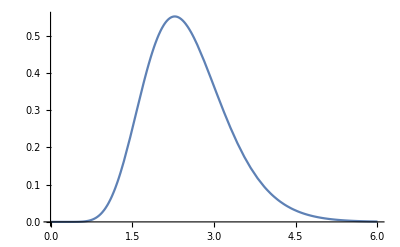

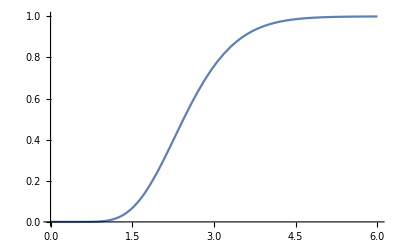

```mathematica
r={3,4,5};
ll={3.4,7.6,4.5};
z=2.5;
GIGpdf[r,ll,z]
GIGcdf[r,ll,z]
(* Dislaying now with 30 digits *)
GIGpdf[r,ll,z,,30]
GIGcdf[r,ll,z,,30]
Plot[GIGpdf[r,ll,x],{x,0,6}]
Plot[GIGcdf[r,ll,x],{x,0,6}]
```

```mathematica
r={2,3,4,7,3};
l={2.3,3.4,4.5,6.7,8.9};
GIGquant[r,l,.95]
GIGquant[r,l,.95,10^-16]
q=GIGquant[r,l,.95,10^-16,20]
GIGcdf[r,l,q]
GIGcdf[r,l,q,,50]
```

5.8395809619

5.839580961856236

5.8395809618562364828

0.95

0.95000000000000000000000000000000000000001800915816

```mathematica
?GIGquant
```

GIGquant [r,  l,  q,  eps,  pp,  ind,  xo,  prec]
Gives the value for the quantile 'q' of a GIG distribution with a set of shape parameters 'r' and rate parameters 'l';
Mandatory arguments:
'r' - list of shape parameters;
'l' - list of rate parameters;
'q' - required quantile (value between 0 and 1);
Optional arguments are:
'eps' - value for the largest difference between consecutive iteration values for the approximate quantile (has a default value of 10^-11);
'pp' - number of digits for printing the quantile value (default value: maximum between 11 and -Log10 of 'eps');
'ind' - index which has a default value of zero and if set to a different value will make the module to take an even more precise path of computation for initial values;
'xo' - initial value for the search of the quantile (default value: 1) and usually there is no need to change this value since the module is sturdy enough to be able to search for good initial values;
'prec' - number of digits used for the intermediate computations in the module (default value: 150)]

```mathematica
r={12,12,14,14,14,14,11,11,11,11,11,13,13,13,13,13,13,13,11,11,11,15,15,14};
l={12.3,13.3,23.4,24.4,25.4,26.4,6.4,7.4,8.4,9.4,10.4,62.3,63.3,64.3,65.3,66.3,67.3,68.3,27.4,28.4,29.4,74.9,75.9,76.9};
GIGquant[r,l,.05,10^-16]
q=GIGquant[r,l,.05,10^-16,20]
GIGcdf[r,l,q]
GIGcdf[r,l,q,,50]
```

12.30539557563194

12.305395575631943474

0.05

0.050000000000000000000000000000000000224377154598878

```mathematica
(***  Examples for the GNIG distribution  ***)
```

```mathematica
?GNIGpdf
```

GNIGpdf[r, r2, ll, ll2, z, prec, precp] gives the value for the pdf of a GNIG distribution with a set of integer shape parameters 'r' and non-integer shape parameter 'r2', and rate parameters 'l', corresponding to the integer shape parameters, and shape parameter 'll2', corresponding to the non-integer shape parameter, computed at the point 'z', computed with precision a precision of 'prec' digits (default value: 150) and displayed with 'precp' digits (default value: 20) - the first 5 arguments are mandatory and the last two are optional

```mathematica
?GNIGcdf
```

GNIGpdf[r, r2, ll, ll2, z, prec, precp] gives the value for the Cdf of a GNIG distribution with a set of integer shape parameters 'r' and non-integer shape parameter 'r2', and rate parameters 'll', corresponding to the integer shape parameters, and shape parameter 'll2', corresponding to the non-integer shape parameter, computed at the point 'z', computed with precision a precision of 'prec' digits (default value: 150) and displayed with 'precp' digits (default value: 20) - the first 5 arguments are mandatory and the last two are optional

0.39533820769315890253

0.18101317358215007971

0.395338207693158902533269355282

0.181013173582150079714094786332

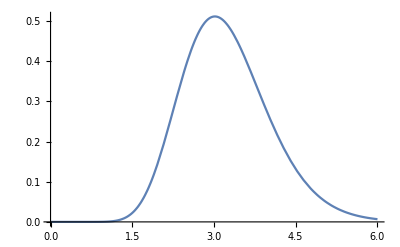

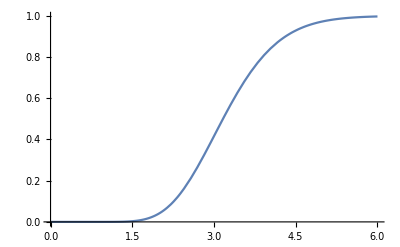

```mathematica
r={3,4,5};
r2=6.4;
ll={3.4,7.6,4.5};
ll2=8.9;
z=2.5;
GNIGpdf[r,r2,ll,ll2,z]
GNIGcdf[r,r2,ll,ll2,z]
(*  Displaying now with 30 digits *)
GNIGpdf[r,r2,ll,ll2,z,,30]
GNIGcdf[r,r2,ll,ll2,z,,30]
Plot[GNIGpdf[r,r2,ll,ll2,x],{x,0,6}]
Plot[GNIGcdf[r,r2,ll,ll2,x],{x,0,6}]
```

```mathematica
?GNIGquant
```

GNIGquant[r  ,r2  ,ll  ,ll2  ,q  ,eps  ,prec  ,xo]
Gives the value for the quantile 'q' of a GNIG distribution with a set of integer shape parameters 'r' and non-integer shape parameter 'r2', and rate parameters 'll' and 'll2', this last one associated with the non-integer shape parameter 'r2';
Mandatory arguments:
'r'   - list of integer shape parameters;
'r2'  - non-integer shape parameter;
'll'  - list of rate parameters associated with the integer shape parameters;
'll2' - rate parameter associated with the non-integer shape parameter;
'q' - required quantile (value between 0 and 1);
Optional arguments are:
'eps' - value for the largest difference between consecutive iteration values for the approximate quantile (has a default value of 10^-11);
'prec' - number of digits of precision for computations and printing the quantile value (default value: maximum between 50 and -Log10 of 'eps');
'xo' - initial value for the search of the quantile (default value: 1) and usually there is no need to change this value since the module is sturdy enough to be able to search for good initial values

```mathematica
r={3,4,5};
r2=6.4;
ll={3.4,7.6,4.5};
ll2=8.9;
GNIGquant[r,r2,ll,ll2,.95]
GNIGquant[r,r2,ll,ll2,.95,10^-16]
q=GNIGquant[r,r2,ll,ll2,.95,10^-16,20]
GNIGcdf[r,r2,ll,ll2,q]
GNIGcdf[r,r2,ll,ll2,q,,50]
```

4.6857879815

4.685787981534263

4.6857879815342626649

0.95

0.95000000000000000000000000000000000000001380390017